```mathematica
x=0.4;
y=0.5;
w=0.3;
h=0.1;
PositiveSlope[u_,v_,x_,y_,w_,h_] :=
{-h,w}.{u,v}+(h*x-w*y) ;
NegativeSlope[u_,v_,x_,y_,w_,h_] :=
{h,w}.{u,v}+(-h*w-h*x-w*y );
```

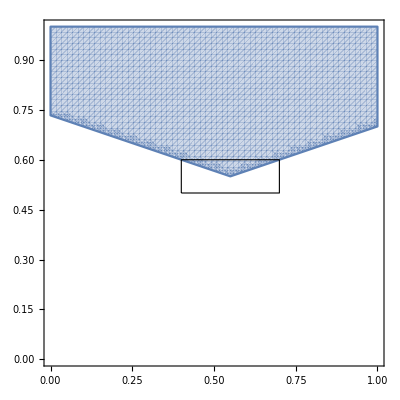

```mathematica
Show[{
RegionPlot[
PositiveSlope[u,v,x,y,w,h]>0&&
NegativeSlope[u,v,x,y,w,h]>0
,{u,0,1},{v,0,1},PlotPoints->60],
Graphics[{
{FaceForm[Opacity[0]],EdgeForm[Black],Rectangle[
{x,y},{x+w,y+h}]}
}]
},Axes->True]
```

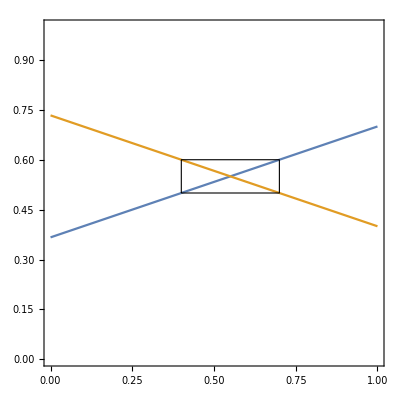

```mathematica
Show[{ContourPlot[
{0==PositiveSlope[u,v,x,y,w,h],
0==NegativeSlope[u,v,x,y,w,h]},
{u,0,1},{v,0,1}
],
Graphics[{
{FaceForm[Opacity[0]],EdgeForm[Black],Rectangle[
{x,y},{x+w,y+h}
]}
}]
},Axes->True]
```

```mathematica
Plot3D[{
0,
PositiveSlope[u,v,x,y,w,h],
NegativeSlope[u,v,x,y,w,h]
},{u,0,1},{v,0,1}]
```

-Graphics3D-

```mathematica
funrect[u_,v_,x_,y_,w_,h_]:= Max[Abs[(h/2)*(u-x)],Abs[(w/2)*(v-y)]];
Manipulate[
ContourPlot[
Min[
funrect[X,Y,0.1,0.1,0.1,0.2],
funrect[X,Y,0.5,0.2,0.2,0.3],
funrect[X,Y,0.9,0.7,0.1,0.1],
funrect[X,Y,0.2,0.8,0.15,0.2]
] == t
,{X,0,1},{Y,0,1},PlotPoints->50],
{{t,0.002},0,0.04}]
```

Some test grid with a hole:

```mathematica
W = {0.6,0.4,0.6,0.4};
H ={0.5,0.6,0.4,0.5};
varW = {w1,w2,w3,w4};
varH = {h1,h2,h3,h4};

Total[Table[varW[[i]]*varH[[i]],{i,1,4,1}]]-1
w1+w2 -1
```

-1+h1 w1+h2 w2+h3 w3+h4 w4

```mathematica
varsW=Array[Subscript[w, #]&,4];
varsH=Array[Subscript[h, #]&,4];
lagrmult = Array[Subscript[λ, #]&,5];
fun = {
Total[Table[varsW[[i]]*varsH[[i]],{i,1,4,1}]]-1,
varsW[[1]]+varsW[[2]]-1,
varsW[[3]]+varsW[[4]]-1,
varsH[[1]]+varsH[[4]]-1,
varsH[[2]]+varsH[[3]]-1
};
(*reg= ImplicitRegion[#^2&@Abs@({Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4],Subscript[h, 1],Subscript[h, 2],Subscript[h, 3],Subscript[h, 4]}-0.5)<0.1,{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4],Subscript[h, 1],Subscript[h, 2],Subscript[h, 3],Subscript[h, 4]}];
dom = Region[reg];)*
```

```mathematica
lagrmult.D[fun,{varsW~Join~varsH}]
```

{h_1 λ_1+λ_2,h_2 λ_1+λ_2,h_3 λ_1+λ_3,h_4 λ_1+λ_3,w_1 λ_1+λ_4,w_2 λ_1+λ_5,w_3 λ_1+λ_5,w_4 λ_1+λ_4}

```mathematica
sol = FindInstance[
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4],Subscript[h, 1],Subscript[h, 2],Subscript[h, 3],Subscript[h, 4]}+lagrmult.D[fun,{varsW~Join~varsH}]=={0.6,0.4,0.6,0.4,0.5,0.6,0.4,0.5}
&&
fun=={0,0,0,0,0},
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4],Subscript[h, 1],Subscript[h, 2],Subscript[h, 3],Subscript[h, 4],Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3],Subscript[λ, 4],Subscript[λ, 5]},5]
```

{{w_1→0.5,w_2→0.5,w_3→0.5,w_4→0.5,h_1→0.5,h_2→0.6,h_3→0.4,h_4→0.5,λ_1→-2.,λ_2→1.1,λ_3→0.9,λ_4→1.,λ_5→1.},{w_1→0.6,w_2→0.4,w_3→0.6,w_4→0.4,h_1→0.55,h_2→0.55,h_3→0.45,h_4→0.45,λ_1→-0.5,λ_2→0.275,λ_3→0.225,λ_4→0.25,λ_5→0.25}}

```mathematica
Drop[sol[[1]],-5]
```

{w_1→0.5,w_2→0.5,w_3→0.5,w_4→0.5,h_1→0.5,h_2→0.6,h_3→0.4,h_4→0.5}